Analiza danych z qc

```mathematica
path = "/Users/jakub/Developer/qc/qc/files/";
outNames = FileNames["*", path<>"outputs"];
files = Table[Flatten@Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
{length, visibility} = Transpose@ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
data =Table[{length[[i]], visibility[[i]], files[[i]]}, {i, 1, Length@length}];
means = Table[{length[[i]], visibility[[i]], Mean[files[[i]]]},{i,1,Length@length}];
```

```mathematica
ByLength=Gather[means, First[#1]==First[#2]&];
```

```mathematica
Table[Last@Transpose[ByLength[[i]]], {i, 1, Length@ByLength}];
```

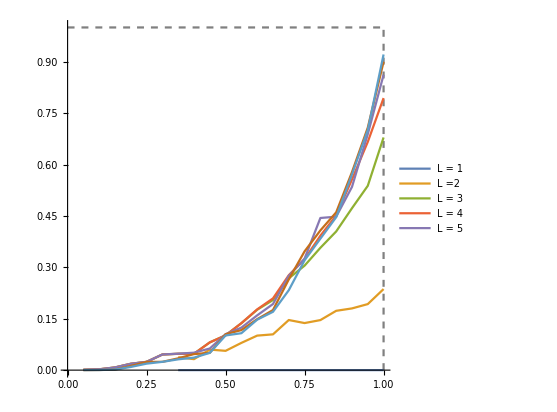

```mathematica
bestT =Table[Last@Transpose[ByLength[[i]]], {i, 1, Length@ByLength}];
visibility = Table[Transpose[ByLength[[i]]][[2]], {i, 1, Length@ByLength}];
plotPoints = Table[Transpose@{visibility[[i]], bestT[[i]]}, {i, 1, Length@visibility}];
plots = Show[ParametricPlot[{x,1}, {x,0,1}, PlotStyle->{Gray,Dashed}],ParametricPlot[{1,y}, {y,0,1}, PlotStyle->{Gray,Dashed}],ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 1", "L =2", "L = 3", "L = 4", "L = 5"},{0.6,0.7}], AxesLabel->{"visibility", "t"}], PlotRange->Full]
```

```mathematica
Export[path<>"figures/tOFetaplot18-07-2021.png", plots, "PNG", RasterSize-> 2000];
```

{1.,0.236549}

```mathematica
Table[plotPoints[[i]][[-2]], {i,1, Length@plotPoints}]
```

{{0.95,2.16023×10^-16},{0.95,0.19272},{0.95,0.537889},{0.95,0.666026},{0.95,0.688668},{0.95,0.707567},{0.95,0.700793}}

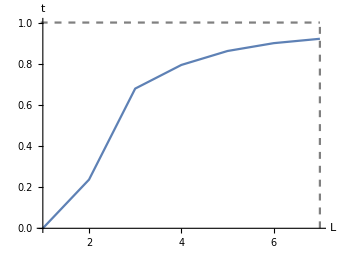

```mathematica
v = -1;
tLpoints = Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}];
tL = Show[ParametricPlot[{x,1}, {x,0,7}, PlotStyle->{Gray,Dashed}, PlotRange->{{1,7},{0,1}}],ParametricPlot[{7,y}, {y,0,1}, PlotStyle->{Gray,Dashed}],ListLinePlot[tLpoints, PlotRange->{{1,7},{0,1}}],AxesLabel->{HoldForm[L],HoldForm[t]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, AspectRatio->0.75]
```

```mathematica
Export[path<>"figures/tOfl-18-07-2021.png", tL, "PNG", RasterSize-> 2000];
```